# Лабораторная работа № 5 Фигурные числа

## Треугольные числа

Треугольное число - есть число точек, которые можно расположить в виде правильного треугольника. 
Иллюстрация показывает, каким образом это можно сделать. 
-Graphics-

Таким образом, последовательность треугольных чисел выглядит следующим образом.
T_1=1
T_2=3
T_3=6
...
T_n=(n(n+1))/2

По сути, если присмотреться к картинкам, каждое треугольное число, есть сумма всех натуральных чисел, ему предшествующих.

### Задание 1

Реализуйте функцию для нахождения n-ого члена последовательности треугольных чисел.

```mathematica
t[n_]:=(n(n+1))/2
```

```mathematica
t[4]
```

10

### Задание 2

Реализуйте функцию для геометрического отображения треугольных чисел. На графическую область нанести текст, аналогично рисунку.

```mathematica
tr[n_]:=NestList[(#+{-1/2,(-√3)/2})&,{1/2#,-(√3)/2#},n-1-#]&/@Range[0,n-1]
```

```mathematica
trGr[n_]:=Graphics[{{Red,PointSize[0.01],Point[#]}&/@Partition[tr[n]//Flatten,2],Blue,PointSize[0.01],Point[#]&/@tr[10][[2]]},ImageSize->800]
```

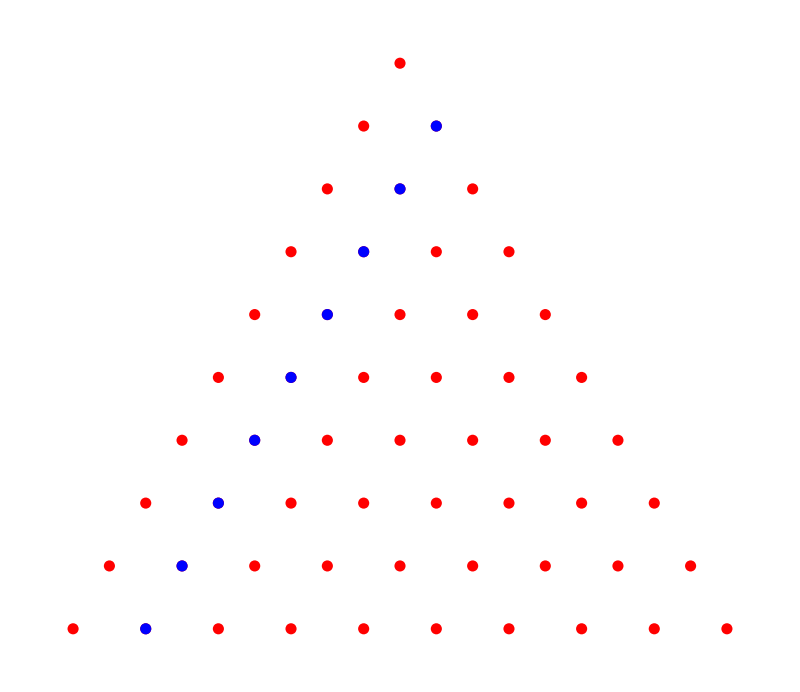

```mathematica
trGr[10]
```

```mathematica
tr[10][[2]]
```

{{1/2,-(√3)/2},{0,-√3},{-1/2,-(3 √3)/2},{-1,-2 √3},{-3/2,-(5 √3)/2},{-2,-3 √3},{-5/2,-(7 √3)/2},{-3,-4 √3},{-7/2,-(9 √3)/2}}

## Квадратные числа

Аналогично определению треугольного числа, можно сформулировать определение квадратного числа.
-Graphics-

### Задание 3

Реализуйте функцию для геометрического отображения квадратных чисел чисел. На графическую область нанести текст, аналогично рисунку.

```mathematica
points[a_List, b_List, n_]:=Join[{a},List[First[a]+#,Last[a]]&/@Range[n-2],{b}]
```

```mathematica
fun[n_]:=Graphics[{PointSize[0.02], RandomColor[], Point/@points[{1, #}, {n,#}, n]&/@Range[n]}, ImageSize->400]
```

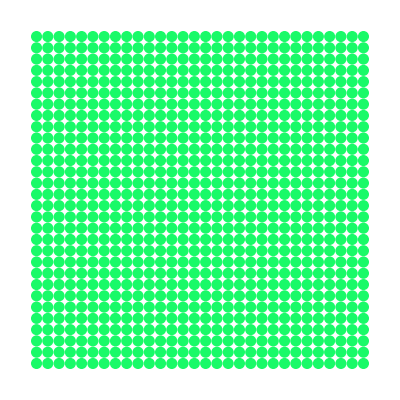

```mathematica
fun[30]
```

```mathematica
points[{1, #}, {10,#}, 10]&/@Range[10]
```

{{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1}},{{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{9,2},{10,2}},{{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{9,3},{10,3}},{{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{9,4},{10,4}},{{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{9,5},{10,5}},{{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{9,6},{10,6}},{{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7},{9,7},{10,7}},{{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8}},{{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9}},{{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10}}}